-Graphics-

{35.083,{0.16064,0.15798,0.15857,0.16021,0.15873,0.15949,0.15987,0.15952,0.15788,0.1594,0.16102,0.15777,0.15944,0.15877,0.15901,0.1598,0.15965,0.15923,0.16167,0.15898,0.15775,0.15959,0.15911,0.16022,0.15787,0.15929,0.15935,0.15855,0.15909,0.15978,0.15932,0.15891,0.15805,0.15764,0.15934,0.16147,0.15643,0.15775,0.15952,0.1595,0.16013,0.16041,0.15958,0.15832,0.15936,0.15951,0.15919,0.15821,0.16031,0.16012,0.16016,0.15997,0.15786,0.1597,0.15865,0.16178,0.15905,0.15816,0.1599,0.15998,0.1599,0.1585,0.15993,0.16064,0.16019,0.15894,0.15841,0.1615,0.1608,0.16226,0.15984,0.1587,0.15897,0.15764,0.1596,0.1591,0.16097,0.16044,0.16102,0.15754,0.15966,0.15596,0.15976,0.15895,0.15957,0.15787,0.15731,0.15778,0.15787,0.15859,0.15861,0.15905,0.16092,0.1588,0.15649,0.1602,0.15682,0.16166,0.15958,0.15817}}

0.15925

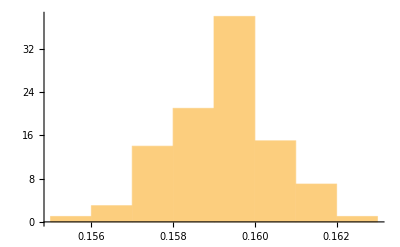

2.548

```mathematica
RegionPlot[x^2+y^3<2&&x+y<1&&y<x^4,{x,-2,2},{y,-2,2},ImageSize->400]
(dataset=Table[nMax=100000;
1.0 (Table[x=RandomReal[{-2,5}];y=RandomReal[{-2,5}];
If[x^2+y^3<2&&x+y<1&&y<x^4,1,0],nMax]//Total)/nMax,{100}])//Timing
Mean[dataset]
Histogram[dataset]
16*Mean[dataset]
```

7.96076

6.04955

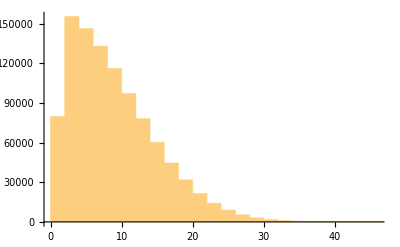

```mathematica
data=Table[dist=RandomChoice[{-1,1},100]//Total//Abs,1000000];
1.0 Mean[data]
1.0 StandardDeviation[data]
Histogram[data]
FindDistribution[data]
```

0.00563

9.99786

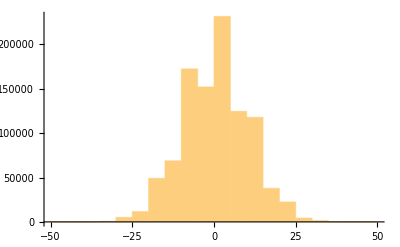

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Pick::incomp: Expressions {SymbolicMachineLearning`PackageScope`estimateBinomial,SymbolicMachineLearning`PackageScope`estimatePoisson,«54»,«60»,«55»,SymbolicMachineLearning`PackageScope`estimateEmpiricalDistribution,SymbolicMachineLearning`PackageScope`estimateHistogramDistribution} and {Indeterminate≥1/7,Indeterminate≥1/7,Indeterminate≥1/7} have incompatible shapes.

Pick::incomp: Expressions {BinomialDistribution[19,0.151621],PoissonDistribution[2.88079],«4»,DataDistribution[Histogram,{{0.0811258,0.0910596,0.0811258,0.089404,0.0877483,0.0695364},{-3.,-1.,1.,3.,5.,7.,9.}},1,302]} and {Indeterminate≥1/7,Indeterminate≥1/7,Indeterminate≥1/7} have incompatible shapes.

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

Pick::incomp: Expressions Pick[{SymbolicMachineLearning`PackageScope`estimateBinomial,SymbolicMachineLearning`PackageScope`estimatePoisson,«54»,«60»,«55»,SymbolicMachineLearning`PackageScope`estimateEmpiricalDistribution,SymbolicMachineLearning`PackageScope`estimateHistogramDistribution},«1»] and {SymbolicMachineLearning`PackageScope`estimateBinomial,SymbolicMachineLearning`PackageScope`estimatePoisson,«54»,«60»,«55»,SymbolicMachineLearning`PackageScope`estimateEmpiricalDistribution,SymbolicMachineLearning`PackageScope`estimateHistogramDistribution}[False] have incompatible shapes.

General::stop: Further output of Pick::incomp will be suppressed during this calculation.

Part::partw: Part 1 of {SymbolicMachineLearning`PackageScope`estimateBinomial,SymbolicMachineLearning`PackageScope`estimatePoisson,«54»,«60»,«55»,SymbolicMachineLearning`PackageScope`estimateEmpiricalDistribution,SymbolicMachineLearning`PackageScope`estimateHistogramDistribution}[] does not exist.

Pick::argtu: Pick called with 1 argument; 2 or 3 arguments are expected.

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

Length::argx: Length called with 0 arguments; 1 argument is expected.

Join::heads: Heads SymbolicMachineLearning`SingleDistributionEstimator and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

AssociationMap::invrp: The argument Join[SymbolicMachineLearning`SingleDistributionEstimator[{-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,«8»,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,«433845»}],{},«1»] is not a valid Association or a list.

Keys::invrl: The argument AssociationMap[SymbolicMachineLearning`file18InformationCriterions`PackagePrivate`criterionvalue[{-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,«433845»},#1,«1»,Log[«1»],Internal]&,«1»] is not a valid Association or a list of rules.

Keys::invrl: The argument AssociationMap is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
data1=Table[dist1=RandomChoice[{-1,1},100]//Total,1000000];
1.0 Mean[data1]
1.0 StandardDeviation[data1]
Histogram[data1]
FindDistribution[data1]
```